```mathematica
对发射波与回波相关运算
```

0.

0.05

0.1

0.15

0.2

0.25

0.3

0.35

0.4

0.45

0.5

0.55

0.6

0.65

0.7

0.75

0.8

0.85

0.9

0.95

1.

1.05

1.1

1.15

1.2

1.25

1.3

1.35

1.4

1.45

1.5

1.55

1.6

1.65

1.7

1.75

1.8

1.85

1.9

1.95

2.

2.05

2.1

2.15

2.2

2.25

2.3

2.35

2.4

2.45

2.5

2.55

2.6

2.65

2.7

2.75

2.8

2.85

2.9

2.95

3.

3.05

3.1

3.15

3.2

3.25

3.3

3.35

3.4

3.45

3.5

3.55

3.6

3.65

3.7

3.75

3.8

3.85

3.9

3.95

4.

4.05

4.1

4.15

4.2

4.25

4.3

4.35

4.4

4.45

4.5

4.55

4.6

4.65

4.7

4.75

4.8

4.85

4.9

4.95

5.

5.05

5.1

5.15

5.2

5.25

5.3

5.35

5.4

5.45

5.5

5.55

5.6

5.65

5.7

5.75

5.8

5.85

5.9

5.95

6.

6.05

6.1

6.15

6.2

6.25

6.3

6.35

6.4

6.45

6.5

6.55

6.6

6.65

6.7

6.75

6.8

6.85

6.9

6.95

7.

7.05

7.1

7.15

7.2

7.25

7.3

7.35

7.4

7.45

7.5

7.55

7.6

7.65

7.7

7.75

7.8

7.85

7.9

7.95

8.

8.05

8.1

8.15

8.2

8.25

8.3

8.35

8.4

8.45

8.5

8.55

8.6

8.65

8.7

8.75

8.8

8.85

8.9

8.95

9.

9.05

9.1

9.15

9.2

9.25

9.3

9.35

9.4

9.45

9.5

9.55

9.6

9.65

9.7

9.75

9.8

9.85

9.9

9.95

10.

10.05

10.1

10.15

10.2

10.25

10.3

10.35

10.4

10.45

10.5

10.55

10.6

10.65

10.7

10.75

10.8

10.85

10.9

10.95

11.

11.05

11.1

11.15

11.2

11.25

11.3

11.35

11.4

11.45

11.5

11.55

11.6

11.65

11.7

11.75

11.8

11.85

11.9

11.95

12.

12.05

12.1

12.15

12.2

12.25

12.3

12.35

12.4

12.45

12.5

12.55

12.6

12.65

12.7

12.75

12.8

12.85

12.9

12.95

13.

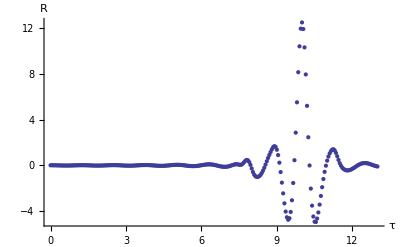

```mathematica
R={};x[t_]:=Sin[5*t]/((t-0.5)^2+0.05);
y[t_]:=(0.2 x[t-10]+RandomReal[]-0.5)*
UnitStep[(t-8)*(12-t)];
signal=Table[{t,y[t]},{t,-5,15,0.02}];
simulating=Interpolation[signal];
Do[corr=NIntegrate[simulating[t]*x[t-τ],
{t,8,12},MaxRecursion->20];
AppendTo[R,{τ,corr}];Print[τ],{τ,0,13,0.05}]
ListPlot[R,PlotRange->All,AxesLabel->{"τ","R"},
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]
Clear[x,y,R,corr,signal,simulating]
```